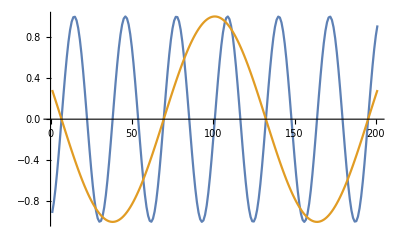

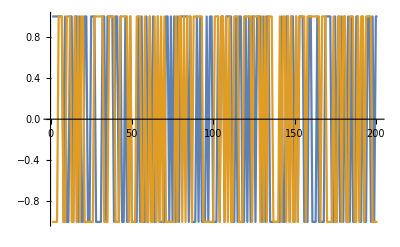

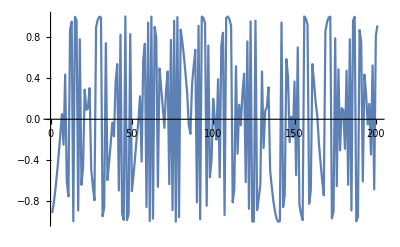

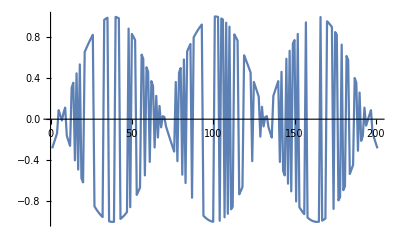

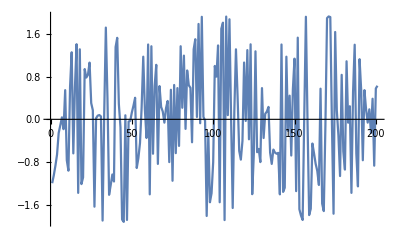

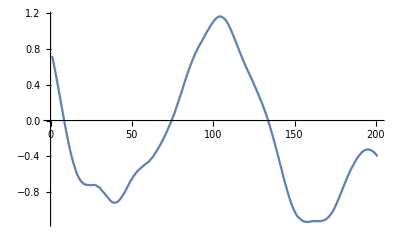

```mathematica
s1[x_]:=Sin[2x];
s2[x_]:=Cos[.5x];

s1p:=Map[s1,Range[-10,10,.1]]
s2p:=Map[s2,Range[-10,10,.1]]

SeedRandom[Round[Pi*Pi]]

c1p:=List[];c2p:=List[];
For[i=-10,i≤10,i+=.1,
c1p=Append[c1p,If[RandomInteger[]==1,1,-1]];
c2p=Append[c2p,If[RandomInteger[]==1,1,-1]];
]


ListLinePlot[{s1p,s2p}]
ListLinePlot[{c1p,c2p}]
a1:=s1p*c1p
ListLinePlot[{a1}]
a2:=s2p*c2p
ListLinePlot[{a2}]
ListLinePlot[{a1+a2}]
ListLinePlot[{LowpassFilter[(a1+a2)*c2p,.1]}]
```